```mathematica
Clear["Global`*"]
(*Defififinition of f=f(x,t)*)
f[x_,t_]= -x + Exp[t];
(*Error message*)
approximate::nonnegativeint="'N' must be replaced by a non-negative integer.";

(*Construction of successively approximate sequences t:time;x0:initial value;N:number of iterations The initial time t0 is always 0*)

approximate[t_,x0_,N_] := Module[{k =0},If[Or[N < 0,Not[IntegerQ[N]]],Message[approximate::nonnegativeint,N],x[0,s_]:=x0;
While[k<N,x[k_,s_]:=(x[k,s] = x0 + Integrate[f[x[k-1,u],u],{u,0,s}]);
k++
];
x[N,t]
]
];
```

```mathematica
approximate[1,1,3]
```

-7/6+ⅇ

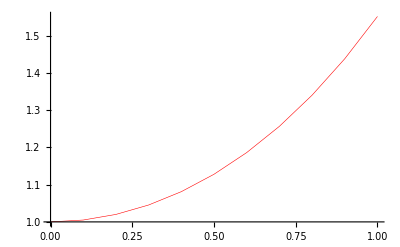

```mathematica
(*Numerical solution (data):k=number of iterations;d=[step size];tlast=[last time]*)nsol[k_,d_,x0_,tlast_]:=Table[{t,approximate[t,x0,k]},{t,0,tlast,d}];
ngraph[k_,d_,x0_,tlast_]:=ListLinePlot[nsol[k,d,x0,tlast],PlotStyle->{Thickness[0.001],RGBColor[1,0,0]},PlotRange->All];
(*Graph of the numerical solution:k=3;d=0:1;x0=1;tlast=10*)
ngraph[3,0.1,1,1]
```

```mathematica
(*Analytical solution:x0=1*)
asol[x0_]:=DSolve[{x '[t]==f[x[t],t],x[0]==x0},x[t],t];
asol[1]
```

{{x[t]→1/2 ⅇ^-t (1+ⅇ^(2 t))}}

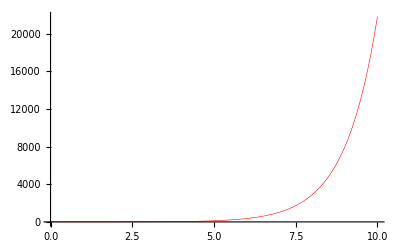

```mathematica
ngraph[3,0.1,1,10]
```

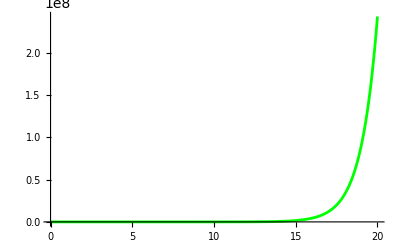

```mathematica
(*Graph of the analytical solution:x0=1;tlast=10*) agraph[x0_,tlast_]:=Plot[Evaluate[x[t]/.asol[x0]],{t,0,tlast},PlotStyle->{Thickness[0.005],RGBColor[0,1,0]},PlotRange->All]
agraph[1,20]
```

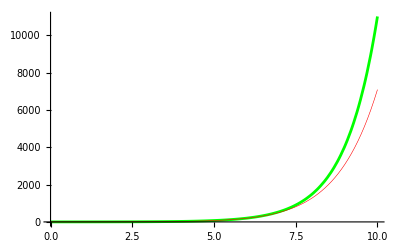

```mathematica
Show[agraph[1,10],ngraph[10,0.1,1,10]]
```

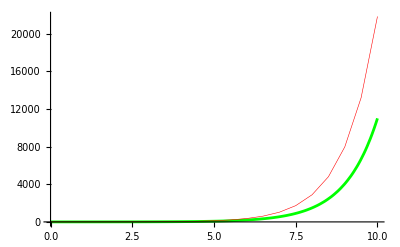

```mathematica
Show[agraph[1,10],ngraph[3,0.5,1,10]]
```

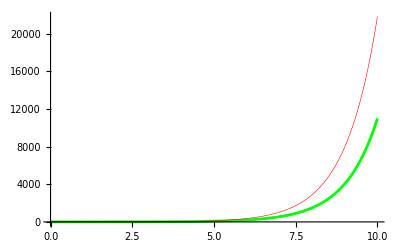

```mathematica
(*k = 3, d = 0.1 , tlast = 10*)
Show[agraph[1,10],ngraph[3,0.1,1,10]]
```

```mathematica
(*k = 3, d = 0.1 , tlast = 10*)
Show[agraph[1,10],ngraph[3,0.1,1,10]]
```